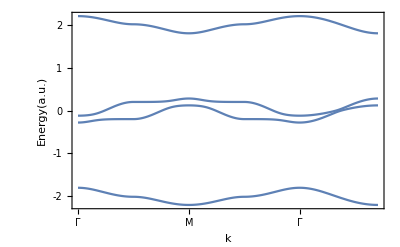

```mathematica
k1f[s_]:=(s-π)HeavisideTheta[π-s]+(s-2π)*HeavisideTheta[2π-s]+(3π-s)*HeavisideTheta[3π-s]+1/(√2)(4π-s)*HeavisideTheta[4π-s]+1/(√2)(s-4π)HeavisideTheta[(4+√2)π-s];
k2f[s_]:=(π-s)HeavisideTheta[π-s]+(s-2π)HeavisideTheta[2π-s]+(s-3π)HeavisideTheta[3π-s]+((4+2 √2)π-(1+1/(√2))s)HeavisideTheta[4π-s]+1/(√2)(s-4π)HeavisideTheta[(4+√2)π-s];
H[t1_,t2_,t3_,k1_,k2_]:=
{{0, t1+2t3(ⅇ^(-ⅈ*k1)+ⅇ^(ⅈ k2)),t2*ⅇ^(-ⅈ*k1),t1-2t3(ⅇ^(-ⅈ*k1)+ⅇ^(-ⅈ*k2))},
{t1-2t3(ⅇ^(ⅈ*k1)+ⅇ^(-ⅈ*k2)),0,t1+2t3(ⅇ^(-ⅈ*k1)+ⅇ^(-ⅈ*k2)),t2 ⅇ^(-ⅈ*k2)},
{t2 ⅇ^(ⅈ*k1),t1-2 t3(ⅇ^(ⅈ*k1)+ⅇ^(ⅈ*k2)),0,t1+2t3 (ⅇ^(ⅈ*k1)+ⅇ^(-ⅈ*k2))},
{t1+2t3 (ⅇ^(ⅈ*k1)+ⅇ^(ⅈ*k2)),t2 ⅇ^(ⅈ k2),t1-2t3 (ⅇ^(-ⅈ*k1)+ⅇ^(ⅈ*k2)),0}};
With[{t1=1.0,t2=0.2,t3=0.01},Plot[Sort[Re[Eigenvalues[N[H[t1,t2,ⅈ*t3,k1f[s*π],k2f[s*π]]]]]],{s,0,(4+√2)},Frame->True,FrameTicks->{{{-2,-1,0,1,2},None},{{0,Γ},{1,Χ},{2,Μ},{3,Σ},{4,Γ},{4+√2,M}}},FrameLabel->{"k","Energy(a.u.)"}]]
```

```mathematica
Export["/Users/Tianqi/Desktop/Research/Notes/Intrinsic SOC/102.eps",%257,"EPS"]
```

/Users/Tianqi/Desktop/Research/Notes/Intrinsic SOC/102.eps

```mathematica
Export["/Users/Tianqi/Desktop/Research/Notes/Intrinsic SOC/108.eps",%252,"EPS"]
```

/Users/Tianqi/Desktop/Research/Notes/Intrinsic SOC/108.eps

```mathematica
Export["/Users/Tianqi/Desktop/Research/Notes/Intrinsic SOC/11.eps",%247,"EPS"]
```

/Users/Tianqi/Desktop/Research/Notes/Intrinsic SOC/11.eps

```mathematica
Export["/Users/Tianqi/Desktop/Research/Notes/Intrinsic SOC/081.eps",%242,"EPS"]
```

/Users/Tianqi/Desktop/Research/Notes/Intrinsic SOC/081.eps